# Лабораторная работа №7

## Часть 1. Задание 1: Элементарная описательная статистика

```mathematica
Mean[{3, 5, 10, 12, 15}] (* среднее значение элементов списка *)
```

9

```mathematica
Moment[{x,y},3](*3-й момент случайной величины списка символов*)
```

1/2 (x^3+y^3)

```mathematica
Median[{3, 5, 1, 12, 15}](* Нахождение медианы *)
```

5

```mathematica
Max[{3, 5, 10, 12, 15}](* Нахождение максимального значения *)
```

15

```mathematica
Variance[{3, 5, 10, 12, 15}](* Нахождение дисперсии *)
```

49/2

```mathematica
StandardDeviation[{3, 5, 10, 12, 15}](* среднеквадратичное отклонения *)
```

7/(√2)

## Задание 2: Работа со статистическими распределениями

NormalDistribution[μ,σ]

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(3 √(2 ⅇ π))

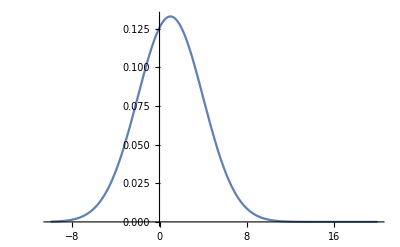

```mathematica
NormalDistribution[μ,σ] (* Нормальное распределение (гауссово), среднее значение μ и стандартное отклонение σ *)
PDF[NormalDistribution[μ,σ],x] (* Получение вероятностей для распределения *)
PDF[NormalDistribution[1,3],4]
Plot[PDF[NormalDistribution[1,3],x],{x,-10,20}] (* Визуализация функции плотности на графике при заданных значениях μ и σ *)
```

17.

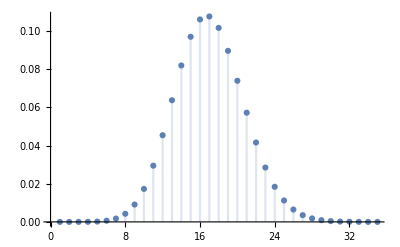

```mathematica
Mean[BinomialDistribution[85,0.2]] (* Среднее значение для 85 попыток при биноминальном распределении с вероятностью успеха 0.2 *)
DiscretePlot[PDF[BinomialDistribution[85,0.2],x],{x,35}, PlotMarkers->Automatic]
```

Log[2]/2

1/2

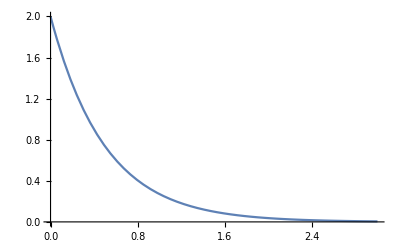

```mathematica
Median[ExponentialDistribution[2]] (*медиана экспоненциального распределения*)
Mean[ExponentialDistribution[2]] (*среднее значение экспоненциального распределения*)
Plot[PDF[ExponentialDistribution[2], x], {x,0, 3}]
```

```mathematica
Mean[DirichletDistribution[{a, b, c}]] 
Mean[DirichletDistribution[{1, 3, 5}]] (*среднее значение распределения Дирихле*)

Plot3D[PDF[DirichletDistribution[{1, 3, 5}], {x, y}], {x, 0, 2}, {y, 0, 2}]
```

{a/(a+b+c),b/(a+b+c)}

{1/9,1/3}

-Graphics3D-

## Задание 3: Проверка гипотез о математическом ожидании

```mathematica
(*дисперсия генеральной совокупности неизвестна*)

data = RandomVariate[NormalDistribution[1,8], 15] (*набор данных*)
```

{-3.5497,-8.05198,-0.183991,-9.53154,7.33606,-13.6408,-8.81536,-23.4759,10.8,2.6593,5.23497,2.80571,-5.21386,8.83172,-0.113652}

```mathematica
(* Выполнение t-теста, при возврате p-значения теста при нулевой гипотезе, что математическое ожидание равно 8 *)
```

```mathematica
TTest[data, 8]
```

0.000755612

```mathematica
(* Выполнение t-теста при альтернативной гипотизе *)
```

```mathematica
TTest[data, 8, AlternativeHypothesis->"Less"]
```

0.000377806

```mathematica
data1 = RandomVariate[NormalDistribution[1,8], 15] (*набор данных*)
```

{3.79929,8.6881,-5.49742,-0.948043,-0.56687,6.91399,19.4039,-4.46158,5.5182,9.51919,9.21938,9.97204,-7.30553,10.5921,-6.4027}

```mathematica
(* t-тест, при котором учитывается равность значений ожиданий наборов данных *)
TTest[{data,data1}]
```

0.0573358

```mathematica
(* t-тест, гласящей что мат.ожидание data в 4 раза больше, чем для data1, с учетом альтернативной гипотизы *)
TTest[{data, data1},4,AlternativeHypothesis->"Less"]
```

0.00147557

## Задание 4: Работа со столбцами данных

```mathematica
(* Блок данных с локализированным генератором псевдослучайных чисел от 1 до 20. 9 записей по 5 чисел в кортеже. SeedRandom - сбрасывает генератор псевдослучайных чисел  *)
```

```mathematica
data = BlockRandom[SeedRandom[];RandomInteger[20,{9,5}]]
```

{{1,9,17,16,20},{11,10,11,16,2},{18,13,6,8,3},{9,7,14,7,6},{14,17,4,11,7},{1,1,20,11,11},{8,3,7,4,18},{19,4,12,14,9},{4,18,15,13,4}}

```mathematica
MatrixForm[data] (* Создание матричной формы *)
```

(1 | 9 | 17 | 16 | 20
11 | 10 | 11 | 16 | 2
18 | 13 | 6 | 8 | 3
9 | 7 | 14 | 7 | 6
14 | 17 | 4 | 11 | 7
1 | 1 | 20 | 11 | 11
8 | 3 | 7 | 4 | 18
19 | 4 | 12 | 14 | 9
4 | 18 | 15 | 13 | 4)

```mathematica
Grid[data] (* Отображение матричной формы без скобок *)
```

1 | 9 | 17 | 16 | 20
11 | 10 | 11 | 16 | 2
18 | 13 | 6 | 8 | 3
9 | 7 | 14 | 7 | 6
14 | 17 | 4 | 11 | 7
1 | 1 | 20 | 11 | 11
8 | 3 | 7 | 4 | 18
19 | 4 | 12 | 14 | 9
4 | 18 | 15 | 13 | 4

```mathematica
Transpose[data](*транспонированная матрица*)
```

{{1,11,18,9,14,1,8,19,4},{9,10,13,7,17,1,3,4,18},{17,11,6,14,4,20,7,12,15},{16,16,8,7,11,11,4,14,13},{20,2,3,6,7,11,18,9,4}}

```mathematica
Mean[data](* Среднее арифметическое каждого столбца *)
StandardDeviation[data] (* Среднеквадратическое отклонение ддя каждого столбца *)
Median[data] (* Поиск медианы для каждой строки *)
```

{85/9,82/9,106/9,100/9,80/9}

{(√(815/2))/3,(√1309)/6,16/3,(√154)/3,(√370)/3}

{9,9,12,11,7}

```mathematica
col =data[[All, 2]](* Получение отдельного столбца *)
Mean[col]
StandardDeviation[col]
```

{9,10,13,7,17,1,3,4,18}

82/9

(√1309)/6

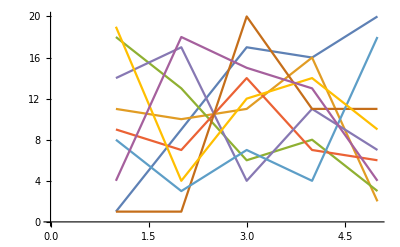

```mathematica
ListLinePlot[data] (* Визуализация группы данных с помощью дмуверного графика (для матриц с более, чем 2-мя столбцами) *)
```

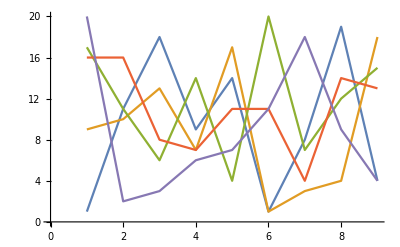

```mathematica
ListLinePlot[ Transpose[data]] (* Визуализация транспонированных данных *)
```

```mathematica
Map[Normalize,Transpose[data]](*нормализация транспонированной матрицы*)
```

{{1/(√1165),11/(√1165),18/(√1165),9/(√1165),14/(√1165),1/(√1165),8/(√1165),19/(√1165),4/(√1165)},{3 √(3/346),5 √(2/519),13/(√1038),7/(√1038),17/(√1038),1/(√1038),√(3/346),2 √(2/519),3 √(6/173)},{17/(6 √41),11/(6 √41),1/(√41),7/(3 √41),2/(3 √41),10/(3 √41),7/(6 √41),2/(√41),5/(2 √41)},{2 √(2/39),2 √(2/39),√(2/39),7/(4 √78),11/(4 √78),11/(4 √78),1/(√78),7/(2 √78),(√(13/6))/4},{√(5/13),1/(2 √65),3/(4 √65),3/(2 √65),7/(4 √65),11/(4 √65),9/(2 √65),9/(4 √65),1/(√65)}}

```mathematica
Transpose[%] (* Транспонирование результата, получив матрицу с нормализованными столбцами (отрабатывает дважды - для столбцов и для строк)*)
```

{{1/(√1165),3 √(3/346),17/(6 √41),2 √(2/39),√(5/13)},{11/(√1165),5 √(2/519),11/(6 √41),2 √(2/39),1/(2 √65)},{18/(√1165),13/(√1038),1/(√41),√(2/39),3/(4 √65)},{9/(√1165),7/(√1038),7/(3 √41),7/(4 √78),3/(2 √65)},{14/(√1165),17/(√1038),2/(3 √41),11/(4 √78),7/(4 √65)},{1/(√1165),1/(√1038),10/(3 √41),11/(4 √78),11/(4 √65)},{8/(√1165),√(3/346),7/(6 √41),1/(√78),9/(2 √65)},{19/(√1165),2 √(2/519),2/(√41),7/(2 √78),9/(4 √65)},{4/(√1165),3 √(6/173),5/(2 √41),(√(13/6))/4,1/(√65)}}

```mathematica
Map[Max,Transpose[data]](* транспонирование и применение преобразований для функций, которые выравнивают свой аргумент *)
```

{19,18,20,16,20}

## Задание 5: Выполнение операций с подгруппами данных

```mathematica
(* Задание урожайности для 3 типов грунта и 2 типов семян *)
(* Задание рождаемости для 3 типов областей и 2 типов населения (urban - городское, rural - сельское) *)
```

```mathematica
data={{brest,urban,945484}, {minsk,urban,803870},{gomel,urban,1062954},{brest,urban,948832},{minsk,urban,810599},{gomel,urban,1064070},{brest,urban,949146},{gomel,urban,1051061},{brest,rural,378543},{minsk,rural,662648},{gomel,urban,1059334},{brest,rural,389212},{gomel,rural,306836},{minsk,rural,664412},{brest,rural,398094},{minsk,rural,661885},{gomel,rural,315952},{brest,rural,405034},{minsk,urban,808934},{gomel,urban,1064070},{gomel,rural,323870}};
```

```mathematica
byCityType=GatherBy[data,First](* Собираем в группы по первому элементу каждой точки данных *)
```

{{{brest,urban,945484},{brest,urban,948832},{brest,urban,949146},{brest,rural,378543},{brest,rural,389212},{brest,rural,398094},{brest,rural,405034}},{{minsk,urban,803870},{minsk,urban,810599},{minsk,rural,662648},{minsk,rural,664412},{minsk,rural,661885},{minsk,urban,808934}},{{gomel,urban,1062954},{gomel,urban,1064070},{gomel,urban,1051061},{gomel,urban,1059334},{gomel,rural,306836},{gomel,rural,315952},{gomel,urban,1064070},{gomel,rural,323870}}}

```mathematica
(* Вывод области и средней рождаемости для каждой группы *)
```

```mathematica
Table[{x[[1,1]],N[Mean[x[[All,-1]]]]},{x,byCityType}]
```

{{brest,630621.},{minsk,735391.},{gomel,781018.}}

```mathematica
(* Группировка данных по второму элементу каждой строки, получаем информацию о рождаемости в зависимости от типа проживающего населения *)
```

```mathematica
byPopulationType=GatherBy[data,#[[2]]&]
```

{{{brest,urban,945484},{minsk,urban,803870},{gomel,urban,1062954},{brest,urban,948832},{minsk,urban,810599},{gomel,urban,1064070},{brest,urban,949146},{gomel,urban,1051061},{gomel,urban,1059334},{minsk,urban,808934},{gomel,urban,1064070}},{{brest,rural,378543},{minsk,rural,662648},{brest,rural,389212},{gomel,rural,306836},{minsk,rural,664412},{brest,rural,398094},{minsk,rural,661885},{gomel,rural,315952},{brest,rural,405034},{gomel,rural,323870}}}

```mathematica
(* Вычисление среднюю рождаемость для каждого типа населения *)
```

```mathematica
Table[{x[[1,2]],N[Mean[x[[All,-1]]]]},{x,byPopulationType}]
```

{{urban,960759.},{rural,450649.}}

```mathematica
(* вычисляем минимальную и максимальную рождаемость для каждого типа населения *)
```

```mathematica
Table[{x[[1,2]],{N[Min[x[[All,-1]]]],N[Max[x[[All,-1]]]]}},{x,byPopulationType}]
```

{{urban,{803870.,1.06407×10^6}},{rural,{306836.,664412.}}}

```mathematica
byCityAndPopulationGroup=GatherBy[data,{First[#],#[[2]]}&] (*группировка по области и типу населения*)
```

{{{brest,urban,945484},{brest,urban,948832},{brest,urban,949146}},{{minsk,urban,803870},{minsk,urban,810599},{minsk,urban,808934}},{{gomel,urban,1062954},{gomel,urban,1064070},{gomel,urban,1051061},{gomel,urban,1059334},{gomel,urban,1064070}},{{brest,rural,378543},{brest,rural,389212},{brest,rural,398094},{brest,rural,405034}},{{minsk,rural,662648},{minsk,rural,664412},{minsk,rural,661885}},{{gomel,rural,306836},{gomel,rural,315952},{gomel,rural,323870}}}

```mathematica
describe[values_]:={Length[values],Mean[values],Median[values],{Min[values],Max[values]}} (* Получение размера выборки, среднего, медианы и диапазона для выбранного списка *)

(* Произведена сортировка по типу населения и области данные отображены в виде таблицы при помощи Grid *)
Table[{x[[1,1]],x[[1,2]],describe[N[x[[All,-1]]]]},{x,byCityAndPopulationGroup}]//Sort//Grid
```

brest | rural | {4,392721.,393653.,{378543.,405034.}}
brest | urban | {3,947821.,948832.,{945484.,949146.}}
gomel | rural | {3,315553.,315952.,{306836.,323870.}}
gomel | urban | {5,1.0603×10^6,1.06295×10^6,{1.05106×10^6,1.06407×10^6}}
minsk | rural | {3,662982.,662648.,{661885.,664412.}}
minsk | urban | {3,807801.,808934.,{803870.,810599.}}

## Задание 6: Замена или удаление недостающих или недействительных данных

```mathematica
(* возврат ввп для каждой страны, внесенной в перечень CountyData *)
```

```mathematica
gdps=Map[CountryData[#,"GDP"]&,CountryData[All]];
```

```mathematica
(* берем первые 10 записей *)
```

```mathematica
Take[gdps,10]
```

{1.98071×10^10 $,Missing[NotAvailable],1.47996×10^10 $,1.45164×10^11 $,6.38×10^8 $,3.15414×10^9 $,6.23069×10^10 $,3.79584×10^8 $,1.41506×10^9 $,3.83067×10^11 $}

```mathematica
(* попытка взять максимум (для некоторых стран эти данные могут быть недоступны) *)
```

```mathematica
Max[gdps]
```

Max::nord2: Comparison of 2.09366×10^13 and -∞ is invalid.

Max[Missing[NotAvailable],2.09366×10^13 $]

```mathematica
(* произведем подсчет Missing данных *)
```

```mathematica
Count[gdps,_Missing]
```

16

```mathematica
(* общее количество данных в наборе *)
```

```mathematica
Length[gdps]
```

249

```mathematica
(* удаление случаев по образцу *)
```

```mathematica
filteredgdps=DeleteCases[gdps,_Missing];
```

```mathematica
{Length[filteredgdps],Max[filteredgdps]}
```

{233,2.09366×10^13 $}

```mathematica
(* задаем новый датасет *)
```

```mathematica
data={{1,17.6,0.2},{2,21.2,3.75},{2,32.5,0.6},{1,54.,3.52},{2,44.5,2.01},{1,75.4,4.12},{3,90.1,1.9},{1,"NA",2.3},{1,64.72,1.2},{1,35.5,3.03}};
```

```mathematica
(* отображение данных в табличной форме *)
```

```mathematica
Grid[data,Dividers->All]
```

1 | 17.6 | 0.2
2 | 21.2 | 3.75
2 | 32.5 | 0.6
1 | 54. | 3.52
2 | 44.5 | 2.01
1 | 75.4 | 4.12
3 | 90.1 | 1.9
1 | NA | 2.3
1 | 64.72 | 1.2
1 | 35.5 | 3.03

```mathematica
(* функция идентифицирует проблемные элементы данных, проверяя соответствие данных заданному шаблону.Она возвращает значение true, если данные на входе не совпадают с шаблоном *)
```

```mathematica
baddata[entry_]:=Not[MatchQ[entry,{1|2,_?NumberQ,_?NumberQ}]]
DeleteCases[data,_?baddata] (* удаление по образцу *)
```

{{1,17.6,0.2},{2,21.2,3.75},{2,32.5,0.6},{1,54.,3.52},{2,44.5,2.01},{1,75.4,4.12},{1,64.72,1.2},{1,35.5,3.03}}

```mathematica
(* задали функцию, определяющую является ли запись набора данных недействительной, путем проверки соответствия первого элемента записи значениям 1 или 2 *)
```

```mathematica
badgroup[entry_]:=Not[MatchQ[entry[[1]],1|2]]
filtereddata=DeleteCases[data,_?badgroup] (* удаление по образцу *)
```

{{1,17.6,0.2},{2,21.2,3.75},{2,32.5,0.6},{1,54.,3.52},{2,44.5,2.01},{1,75.4,4.12},{1,NA,2.3},{1,64.72,1.2},{1,35.5,3.03}}

```mathematica
(* выборка данных элементов группы 1 *)
```

```mathematica
group1=Select[filtereddata,#[[1]]===1&]
```

{{1,17.6,0.2},{1,54.,3.52},{1,75.4,4.12},{1,NA,2.3},{1,64.72,1.2},{1,35.5,3.03}}

```mathematica
(* выборка чисел из последнего элемента каждой записи (2 столбец), рассчет среднего значения *)
```

```mathematica
group1mean=Mean[Select[group1[[All,2]],NumberQ]]
```

49.444

```mathematica
(* подставление вместо NA найденное среднее значение *)
```

```mathematica
filtereddata[[All,2]]=filtereddata[[All,2]]/."NA"->group1mean
```

{17.6,21.2,32.5,54.,44.5,75.4,49.444,64.72,35.5}

```mathematica
(* отображение отфильтрованных данных таблично *)
```

```mathematica
Grid[filtereddata,Dividers->All]
```

1 | 17.6 | 0.2
2 | 21.2 | 3.75
2 | 32.5 | 0.6
1 | 54. | 3.52
2 | 44.5 | 2.01
1 | 75.4 | 4.12
1 | 49.444 | 2.3
1 | 64.72 | 1.2
1 | 35.5 | 3.03

## Задание 7: Выполнение линейной регрессии

```mathematica
(* формирование набора данных *)
```

```mathematica
data = Table[{2 + i + RandomReal[{-2, 10}], i + RandomReal[{-2, 6}]}, {i, 1, 20}];model=LinearModelFit[data,x,x] (* создание линейной модели заданного набора данных *)
```

FittedModel[0.967263+0.705944 x]

```mathematica
model["BestFit"] (* извлечение функциональной формы модели *)
```

0.967263+0.705944 x

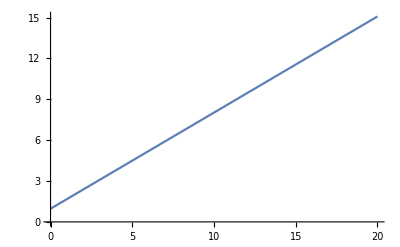

```mathematica
Plot[model["BestFit"], {x, 0, 20}] (* визуализация функциональной формы модели *)
```

```mathematica
(* отображение данных и линии наилучшего соответствия *)
```

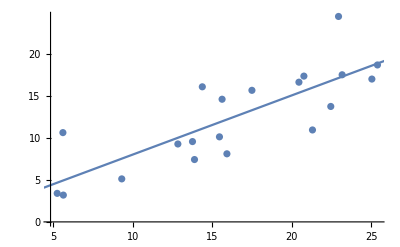

```mathematica
Show[ListPlot[data], Plot[model["BestFit"], {x, 0, 30}]]
```

```mathematica
model["ParameterTable"] (* получаем информацию по оценке параметров выполненной регрессии (оценка) *)
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.967263 | 2.13455 | 0.453146 | 0.655859
x | 0.705944 | 0.122095 | 5.7819 | 0.0000176699

```mathematica
(* отображение нормализованных и наблюдаемых невязок *)
```

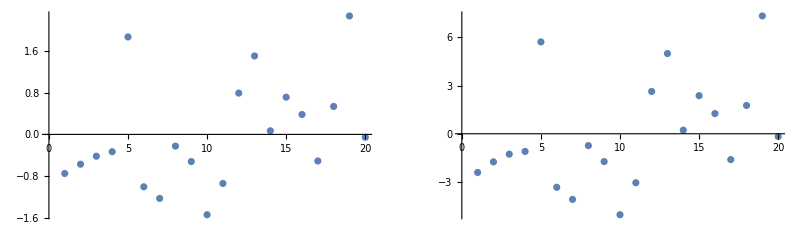

```mathematica
{sr,fr}=model[{"StandardizedResiduals", "FitResiduals"}];
{{ListPlot[sr], ListPlot[fr]}}//GraphicsGrid
```

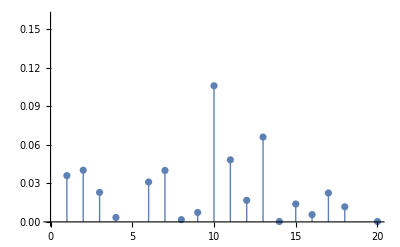

```mathematica
ListPlot[model["CookDistances"], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick] (* график расстояний Кука *)
```

## Часть 2. Задание: моделирование методом Монте-Карло

{-0.231641,1.28191,-1.66574,0.750311,2.45596,0.985974,0.0926135,-1.2889,-0.656466,0.180195,0.0780097,0.201289,-0.287647,-1.48885,0.968089,-0.449432,-2.56146,-1.03782,1.05863,1.48402,-2.28964,0.767972,-1.43986,0.214147,-0.318874,-1.11465,0.600097,-0.249462,0.446976,-0.515928}

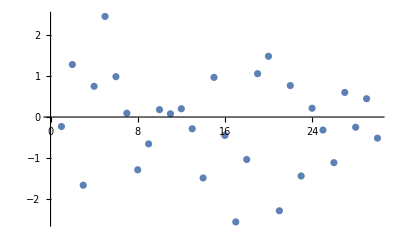

```mathematica
norms1=RandomVariate[NormalDistribution[0,1],30] (*последовательность из 30 чисел по нормальному распределению,со средним 0 и стандартным отклонением 1*)
ListPlot[norms1]
```

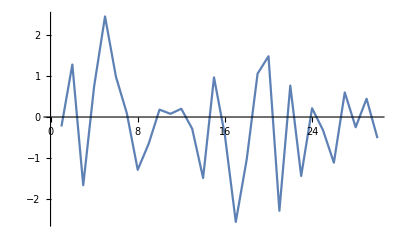

```mathematica
ListLinePlot[norms1](*график случайного блуждания*)
```

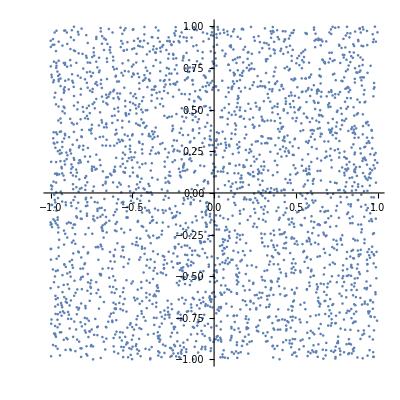

```mathematica
pairs=RandomReal[{-1,1},{3000,2}]; (*Сгенерация 3 000 точек в квадрате,ограниченном значениями{-1,-1}и{1,1}:*)
lp=ListPlot[pairs,AspectRatio->1]
```

```mathematica
Histogram3D[pairs,Automatic,"ProbabilityDensity"](*Визуализируем плотность распределения точек*)
```

-Graphics3D-